# Reversible Timestamp Blurring for Spill Data

## The dts1 transform: specification, reference implementation and verification

This notebook document the process that is being used to “blur” the timestamp data that is generated by the darpa-spill-dump command.  The actual utility is part of the general DARPA-SpillServer package that is homed in the NOvADAQ git repository (but specifically Andrew’s modern git repo not the older one that we generated a long time ago from the SVN repo.

Things to be aware of:
This document as well as the mathematica library files (the .wl files) all live in the docs area of the repository.  You need both build_notebook.wl and dts1.wl to fully build this notebook.

I have an older version of mathematica so this is only tested on Mathematica 12 but it should work on more modern versions.  The translation of this to the python code is portable to any modern python > 3.12

And this was originally put together in Oct 2026 so that give a feel for when it was last looked at.

## 1. Purpose/Problem

The END (Experimental Neutrino Detector) needs timestamps from the NOvA timing system to trigger/constrain their detector data.  But for some unknown reason we were told that if the spill data was presented in its natural form and resolution then it could be considered CUI (I’ve had my CUI training and....no that is manifestly incorrect but we don’t disobey orders)  The solution is apparently to degrade or obscure the true NuMI beam time.

So our solution is the following -- we are going to shift the actual beam spill time (based on the NOvAtime clock which is directly sync’d to GPS but runs at a 64MHz clock) by a small amount.  But we need to do so in a way that we can recover the actual time.  In this manner we can transfer and store beamtime data to external entities and then give them a procedure to decrypt/de-blur the times for real analysis.

The Requirements I was  given/imposed were:

Assume a start from the output of darpa-spill-dump (CSV or JSON) ( this is the original source of truth)

Shift each event's timestamp by a random offset in either a  positive or negative direction.

The actual distribution that the offsets are pulled from should be random variate  using either a flat distribution or Gaussian PDF (and really we could do any smooth PDF, but they wanted flat and Gauss)

The process should be fully reproducible.  So we are using deterministic tokens and seeds instead of something like a thermal rng or a time seeded on.

The transform should be fully  invertible with only knowledge of the original token and the data value

The amount of blur should be tunable by the user but we also want to cap it so we don’t spin off into some infinity in the tails of a distribution.

So this notebook defines the transform (version dts1), gives a reference implementation, proves and tests its invertibility, characterises the variates, and examines what the blur does and does not hide. It is the specification the Python implementation (darpa_spillserver.shift, command darpa-spill-shift) is tested against.

## 2. Setup

```mathematica
Get[FileNameJoin[{If[ValueQ[$DTS1Dir], $DTS1Dir, FileNameJoin[{NotebookDirectory[], "shift"}]], "dts1.wl"}]];
$dataDir = If[ValueQ[$DTS1Dir], $DTS1Dir, FileNameJoin[{NotebookDirectory[], "shift"}]];
```

Define the nova clock frequency (64MHz) and maximum offset in nova clock ticks

```mathematica
{$Ticks, $MaxOffset}
```

{64000000,32000000}

One second is 64000000 ticks; the largest permitted bound, 500 ms, is 32000000 ticks.  When a shift is computed it is computed in an integer number of ticks so that everything remains on the same clock freq.

## 3. Input Data Format (and what to transform)

The dump format of our input data has the timestamp in different representations (NOvA time, GPS time, UTC etc....)  Moving nova_time alone would leave the true time readable from the others, so each must be considered.

So we read in a file and then split it up to work with it

```mathematica
sample = Import[FileNameJoin[{$dataDir, "sample_2026-10-12T0000_10min.csv"}], "CSV"];
sample = Select[sample, StringQ[#[[1]]] =!= True || !StringStartsQ[#[[1]], "#"] &];
header = First[sample];
rows = AssociationThread[header -> #] & /@ Rest[sample];
Length[rows]
```

4701

```mathematica
TableForm[Values /@ rows[[;; 6]], TableHeadings -> {None, header}]
```

nova_time | spill_type_name | source | event_number | delta | pps_offset
33885388992000001 | BNB | tdu-near-master-ppc-02 | 178098 | 64000000 | 1
33885388992000002 | BNB | tdu-near-master-ppc-03 | 178094 | 64000000 | 2
33885388992001413 | ACCEL_ONE_HZ_TCLK | tdu-near-master-ppc-01 | 1219019 | 64001409 | 1413
33885389019521752 | BNB_TCLK | tdu-near-master-ppc-01 | 1219020 | 27520339 | 27521752
33885389023789974 | BNB_TCLK | tdu-near-master-ppc-01 | 1219021 | 4268222 | 31789974
33885389028058203 | BNB_TCLK | tdu-near-master-ppc-01 | 1219022 | 4268229 | 36058203

utc, gps, unix_* and the other time columns are functions of nova_time and are simply recomputed from the shifted value. Two columns are not:

```mathematica
Counts[(#["pps_offset"] - Mod[#["nova_time"], $Ticks]) & /@ rows]
```

<|0→4701|>

pps_offset is exactly tT on every row: the sub-second phase of the true time. Left alone it would undo any blur below one second.

```mathematica
byKey = Association[(#["source"] -> #["event_number"]) -> #["nova_time"] & /@ rows];
Counts[Map[With[{p = byKey[#["source"] -> #["event_number"] - 1]},
     Which[MissingQ[p], "predecessor not in file",
      #["delta"] == #["nova_time"] - p, "delta = t(n) - t(n-1)", True, "other"]] &, rows]]
```

<|predecessor not in file→612,delta = t(n) - t(n-1)→4089|>

delta is the gap to the previous hardware event on the same TDU, t_n-t_(n-1), where n is event_number. Chained from any one known time it would give back every other. On ppc-01 about 19% of predecessors are events the archive never stored, so delta cannot simply be recomputed from neighbouring rows. (Over 1,052,663 rows on 12–13 October 2026 the same two relations hold without exception.)

## 4. The idea

Each time sample is tied to a specific TDU and has a specific event number tag.  The combination of the tdu source ID and the event number then gives a unique key for each event.  You can then define the transform  ℱ(source, evt_no, crypt) and ℱ^-1(source, evt_no, crypt), the source and event number can be passed openly via the data file and then a single cryptographic key can be passed separately for the entire data set.

 Using this method we want only a simple shift then we note that ℱ = -ℱ^-1 which makes the forward and back transforms trivial.  To forward transform we just add the computed offset, to invert it we subtract the offset and nothing more than the event number, source and token are needed:

t'_n==t_n+o_n

t_n==t'_n-o_n

The other strength of this approach is that because there is no dependance or relation between o_nand  o_(n+1) the process is well defined even if data is missing from the datafile or even if the file is scrambled.   This even applies to the time deltas between samples (since you can just add or sub the offset) :

Δ'_n==Δ_n+o_n-o_(n-1)

p'_n==(p_n+o_n)T

Each is a bijection with an explicit inverse, Δ_n==Δ'_n-o_n+o_(n-1) and p_n==(p'_n-o_n)T (the latter because 0≤p_n<T). When event n-1 is present, Δ'_n==t'_n-t'_(n-1) exactly, so the shifted file is self-consistent. None of this depends on how the TDU defines the columns: the inverse is algebraic.

## 5. Specification of dts1 algorithm and implementation

#### This is the description of the algorthim

### 5.1 The Token

The encryption token that we are going to use is actually going to carry more information in it then just a random seed value.  What we do is construct and pass a token that carries the random variate distribution, its actual parameters (in the NOvA time base ticks), and a 256-bit secret K.  So the form of the token looks like:

dts1:flat:a=A:<64 hex digits>
dts1:gauss:sigma=S:cut=C:<64 hex digits>

Where “flat” represents a flat box distribution and “gauss” represents a Gaussian with width sigma and maximum tail that is truncated by the cut.  The hex digits are the key value.  Holding the token is sufficient to both encode and invert. The part before the secret is the parameter string P, which is public and is mixed into every keyed block so that the same secret with different parameters gives unrelated offsets. And we constrain the parameters such that the width of the box A i 1≤A≤32000000; S≥1, S/2≤C≤32000000.

K is either 32 random bytes, or derived from a user seed with PBKDF2-HMAC-SHA256 (RFC 8018), with salt darpa-spill-shift/dts1, 600,000 iterations.  We aren’t overly worried about anyone wanting to “break” this, but a seed while convenient and reproducible is only as strong as the actual seed that is chosen (if you are using the SHA hash).  So basically if an attacker who can guess that you used your dog’s name....well they can invert the data.

The other thing to note is that a “public fingerprint”, the first 64 bits of HMAC(K,"dts1 fingerprint|"<>P), is written into shifted files so that inversion with the wrong token screws this up and allows you to detect that you used the wrong decryption token rather than silently producing wrong times. And no it doesn’t reveals anything about about the real K that was used.

So mint some tokens:

```mathematica
tokF = makeToken[<|"dist" -> "flat", "a" -> 3200000|>, ByteArray[Normal@Hash["dts1 test vector", "SHA256", "ByteArray"]]]
```

dts1:flat:a=3200000:647f5c2495a4451550bd0faf3e4a0d7d8c5af77e26ec2a726a5a09660e7c78f2

```mathematica
tokG = makeToken[<|"dist" -> "gauss", "sigma" -> 1280000, "cut" -> 3840000|>, ByteArray[Normal@Hash["dts1 test vector", "SHA256", "ByteArray"]]]
```

dts1:gauss:sigma=1280000:cut=3840000:647f5c2495a4451550bd0faf3e4a0d7d8c5af77e26ec2a726a5a09660e7c78f2

```mathematica
{fingerprint[tokF], fingerprint[tokG]}
```

{7a63e2a2874c456f,42005a1faeae05cd}

These two tokens, flat ±50 ms and Gaussian σ = 20 ms cut at 3σ = 60 ms, are used throughout. Their secret is the SHA-256 of a public string: test tokens only.

### 5.2 Keyed blocks

For event n of source s, block j is

B_j==HMAC("SHA-256",K,P<>"|"<>s<>"|"<>n<>"|"<>j)

with n and j as signed decimal integers. HMAC-SHA256 is a pseudorandom function: without K its outputs are indistinguishable from independent uniform bytes, and knowing any number of offsets does not help predict another. Check against RFC 4231, test case 2:

```mathematica
StringJoin[IntegerString[Normal@hmacSHA256[StringToByteArray["Jefe"], "what do ya want for nothing?"], 16, 2]] ==
 "5bdcc146bf60754e6a042426089575c75a003f089d2739839dec58b964ec3843"
```

True

### 5.3 Flat variate

Read the first 16 bytes of B_0 as a big-endian integer X and take

o_n==X(2 A+1)-A

This is uniform on the 2 A+1 integers -A≤o≤A up to a bias below (2 A+1)/2^128, about 1.9×10^(−31) at the largest A. It uses integer arithmetic only, so every implementation on every platform produces the identical offset.

### 5.4 Gaussian variate

Split each block into four 64-bit big-endian words w. Each gives an exact dyadic uniform

u==(Floor[w/2^11]+1/2)/2^53

strictly inside (0, 1) and exactly representable as a double. The standard normal variate is x==Φ_AS241^(-1(u)), Wichura's algorithm AS241 (PPND16, Applied Statistics 37, 1988), a rational approximation with relative error near 10^(−16). Draws are taken in order, block j = 0, 1, 2, …, word 0–3, and the first with Abs[x] S≤C is used:

o_n==Round[x S]

Rejection gives the exact normal truncated to ±C without needing erf anywhere. Round is to the nearest integer, ties to even. The constraint C≥S/2 keeps the acceptance probability above 38%, so the 256 draws available are never exhausted in practice (failure probability below 10^(−53)).

Exactness. The specification is AS241 evaluated in exact real arithmetic on the exact coefficients; this reference evaluates it at 60 digits. A double-precision evaluation agrees except when x S lies within about 10^(−7) ticks of a rounding boundary or of ±C; there the Python implementation recomputes in decimal at 50 digits. That makes the offset, and so the inversion, identical on every machine, which a plain floating-point evaluation (whose Log may differ by an ulp between C libraries) would not guarantee. Section 8 constructs such near-tie cases deliberately.

## 6. The flat variate

```mathematica
flat = Table[offset[tokF, "tdu-test", n], {n, 20000}];
{Min[flat], Max[flat], N[Mean[flat]], N[StandardDeviation[flat]], N[Sqrt[((2*3200000 + 1)^2 - 1)/12]]}
```

{-3199164,3199992,1982.83,1.8491×10^6,1.84752×10^6}

Range, mean, standard deviation and the exact standard deviation √(1/12 ((2 A+1)^2-1)) of the discrete uniform on ±A. In milliseconds the bound is 50 ms and σ = 28.9 ms.

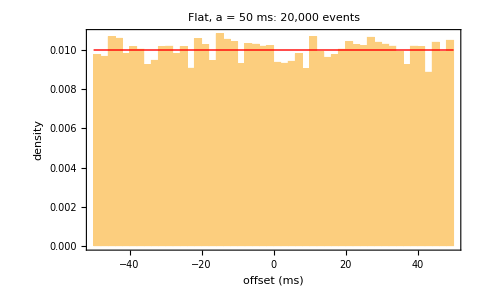

```mathematica
Histogram[flat/64000., {-50, 50, 2}, "PDF", Frame -> True, FrameLabel -> {"offset (ms)", "density"},
 PlotLabel -> "Flat, a = 50 ms: 20,000 events", ImageSize -> 480,
 Epilog -> {Red, Line[{{-50, 1/100}, {50, 1/100}}]}]
```

```mathematica
PearsonChiSquareTest[flat, DiscreteUniformDistribution[{-3200000, 3200000}], "TestDataTable"]
```

| Statistic | P-Value
Pearson χ^2 | 103.727 | 0.516812

## 7. The Gaussian variate

### 7.1 AS241 accuracy

```mathematica
errs = Table[With[{u = uniformFromWord[RandomInteger[2^64 - 1]]},
    {N[InverseCDF[NormalDistribution[], u], 30],
     N[(as241[u] - InverseCDF[NormalDistribution[], u])/Max[1, Abs[InverseCDF[NormalDistribution[], u]]], 30]}], {3000}];
N[Max[Abs[errs[[All, 2]]]]]
```

7.42979×10^-17

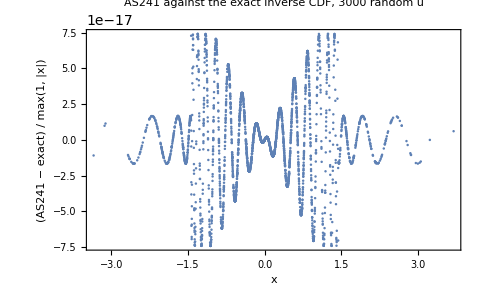

```mathematica
ListPlot[errs, Frame -> True, FrameLabel -> {"x", "(AS241 − exact) / max(1, |x|)"},
 PlotLabel -> "AS241 against the exact inverse CDF, 3000 random u", ImageSize -> 480, PlotRange -> All]
```

The worst relative error is 10^(−16) in size. At σ = 500 ms, the largest allowed, that is below 10^(−8) ticks: AS241 is indistinguishable from the exact normal at the resolution of the clock.

### 7.2 Sampling

```mathematica
gauss = Table[offsetGauss[parseToken[tokG]["secret"], "dts1:gauss:sigma=1280000:cut=3840000", 1280000, 3840000, "tdu-test", n], {n, 20000}];
{Min[gauss[[All, 1]]], Max[gauss[[All, 1]]], N[Mean[gauss[[All, 1]]]], N[StandardDeviation[gauss[[All, 1]]]]}
```

{-3828386,3839899,9896.41,1.26102×10^6}

```mathematica
sigmaTrunc[k_] := Sqrt[1 - 2 k PDF[NormalDistribution[], k]/(2 CDF[NormalDistribution[], k] - 1)];
N[1280000 sigmaTrunc[3]]
```

1.26282×10^6

The standard deviation of a unit normal truncated at ±k is √(1-(2 k ϕ(k))/(2 Φ(k)-1)); at k==3 the expected value in ticks is above, matching the sample.

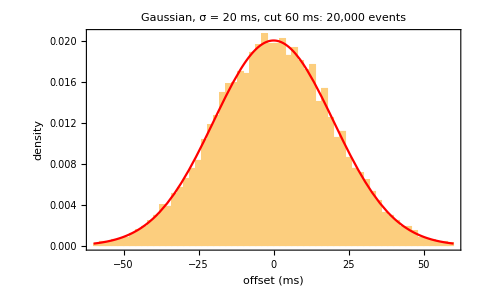

```mathematica
Histogram[gauss[[All, 1]]/64000., {-60, 60, 2}, "PDF", Frame -> True,
 FrameLabel -> {"offset (ms)", "density"}, PlotLabel -> "Gaussian, σ = 20 ms, cut 60 ms: 20,000 events", ImageSize -> 480] ~Show~
 Plot[PDF[TruncatedDistribution[{-60, 60}, NormalDistribution[0, 20]], t], {t, -60, 60}, PlotStyle -> Red]
```

```mathematica
KolmogorovSmirnovTest[N@gauss[[All, 2]], TruncatedDistribution[{-3, 3}, NormalDistribution[]], "TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.00619559 | 0.426432

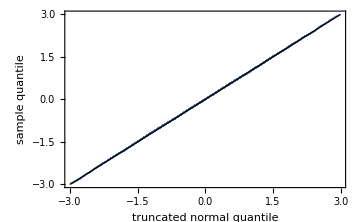

```mathematica
QuantilePlot[N@gauss[[All, 2]], TruncatedDistribution[{-3, 3}, NormalDistribution[]], ImageSize -> 360,
 Frame -> True, FrameLabel -> {"truncated normal quantile", "sample quantile"}]
```

```mathematica
{N[Mean[gauss[[All, 3]]]], N[1/(2 CDF[NormalDistribution[], 3] - 1)], Max[gauss[[All, 3]]]}
```

{1.00325,1.00271,3}

Mean draws per event, its expectation 1/(2 Φ(3)-1), and the most any event needed.

## 8. Determinism near rounding boundaries

Offsets near a half-tick are where floating point could disagree between machines. Search the 53-bit grid around chosen half-integers x S==m+1/2 for the uniforms that land closest:

```mathematica
nearTie[S_, mm_] := Module[{x0 = (mm + 1/2)/S, k0, cands},
   k0 = Floor[CDF[NormalDistribution[], N[x0, 50]] 2^53 - 1/2];
   cands = Table[With[{u = (k + 1/2)/2^53}, {k, N[as241[u] S, 40]}], {k, k0 - 3, k0 + 3}];
   First@SortBy[cands, Abs[FractionalPart[Abs[#[[2]]]] - 1/2] &]];
ties = Table[With[{r = nearTie[1280000, mm]}, <|"sigma" -> 1280000, "k" -> r[[1]],
     "xS" -> ToString[NumberForm[r[[2]], 30, ExponentFunction -> (Null &)]], "distance_from_half" -> N[Abs[FractionalPart[Abs[r[[2]]]] - 1/2]],
     "offset" -> Round[r[[2]]]|>], {mm, {12345, -400000, 1000000, -2500000, 3000000, 77}}];
TableForm[Values /@ ties, TableHeadings -> {None, Keys[First[ties]]}]
```

sigma | k | xS | distance_from_half | offset
1280000 | 4538256695243178 | 12345.5000000000932663359407183 | 9.32663×10^-11 | 12346
1280000 | 3398690367348873 | -399999.499999999847667264435734 | 1.52333×10^-10 | -399999
1280000 | 7049686070390478 | 1000000.49999999980907333613196 | 1.90927×10^-10 | 1000000
1280000 | 228804620516296 | -2499999.49999999995262166969265 | 4.73783×10^-11 | -2499999
1280000 | 8921221290600054 | 3000000.49999999871584781628149 | 1.28415×10^-9 | 3000000
1280000 | 4503817193641715 | 77.5000000001629020829743627687 | 1.62902×10^-10 | 78

Distances of 10^(−10) ticks and below are far inside the error of a double-precision evaluation. The Python implementation detects these and falls back to exact decimal arithmetic; these cases are among its test vectors.

## 9. Inversion on real data

The sample is ten minutes from the Near Detector, 2026-10-12 00:00–00:10 UTC: three TDUs, 4701 events. Shift it with each token, then invert, and compare every transformed column.

```mathematica
toRow[r_] := <|"nova_time" -> r["nova_time"], "source" -> r["source"],
    "event_number" -> r["event_number"], "delta" -> r["delta"], "pps_offset" -> r["pps_offset"]|>;
orig = toRow /@ rows;
shiftedF = shiftRow[tokF, #] & /@ orig;
shiftedG = shiftRow[tokG, #] & /@ orig;
{invertRow[tokF, #] & /@ shiftedF === orig, invertRow[tokG, #] & /@ shiftedG === orig}
```

{True,True}

Both round trips are exact on all 4701 rows and all columns. The shifted files are self-consistent: wherever event n-1 is present, Δ'_n equals the gap between the shifted times, and p'_n equals the shifted phase.

```mathematica
consistent[sh_] := Module[{bk = Association[(#["source"] -> #["event_number"]) -> #["nova_time"] & /@ sh]},
   Counts[Map[With[{p = bk[#["source"] -> #["event_number"] - 1]},
      If[MissingQ[p], "no predecessor", #["delta"] == #["nova_time"] - p]] &, sh]]];
{consistent[shiftedG], Counts[(#["pps_offset"] == Mod[#["nova_time"], $Ticks]) & /@ shiftedG]}
```

{<|no predecessor→612,True→4089|>,<|True→4701|>}

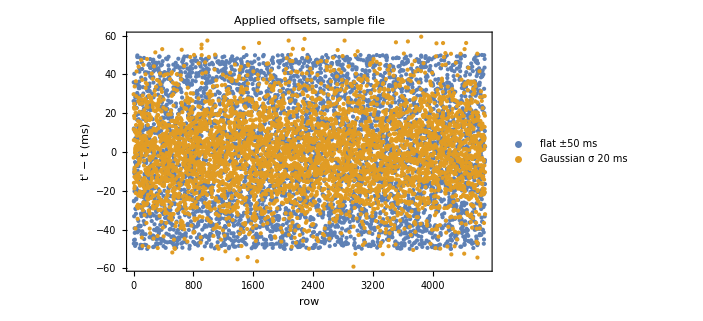

```mathematica
ListPlot[{(shiftedF[[All, "nova_time"]] - orig[[All, "nova_time"]])/64000.,
  (shiftedG[[All, "nova_time"]] - orig[[All, "nova_time"]])/64000.}, Frame -> True,
 FrameLabel -> {"row", "t' − t (ms)"}, PlotLegends -> Placed[{"flat ±50 ms", "Gaussian σ 20 ms"}, Below],
 PlotLabel -> "Applied offsets, sample file", ImageSize -> 520, PlotStyle -> PointSize[Small]]
```

### 9.1 The wrong token

Inverting with a token that differs in one bit of the secret gives times that are wrong by the difference of two independent offsets, with no visible sign of failure. Hence the fingerprint check.

```mathematica
flip[tok_] := Module[{p = parseToken[tok], k}, k = Normal[p["secret"]]; k[[1]] = BitXor[k[[1]], 1];
   makeToken[KeyDrop[p, "secret"], ByteArray[k]]];
wrongTok = flip[tokF];
{fingerprint[tokF], fingerprint[wrongTok]}
```

{7a63e2a2874c456f,f07f54427077f463}

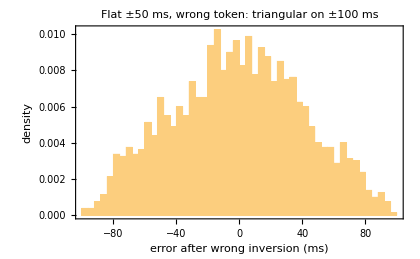

```mathematica
bad = invertRow[wrongTok, #] & /@ shiftedF[[;; 2000]];
Histogram[(bad[[All, "nova_time"]] - orig[[;; 2000, "nova_time"]])/64000., {-100, 100, 4}, "PDF",
 Frame -> True, FrameLabel -> {"error after wrong inversion (ms)", "density"}, ImageSize -> 420,
 PlotLabel -> "Flat ±50 ms, wrong token: triangular on ±100 ms"]
```

## 10. Independence and key sensitivity

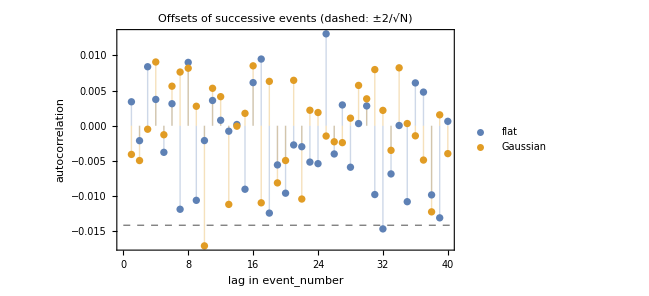

```mathematica
acf[v_, maxlag_] := With[{z = v - Mean[v]}, Table[Total[Most[RotateLeft[z, l]] z[[;; -2]]]/Total[z^2], {l, 1, maxlag}]];
ListPlot[{acf[N@flat, 40], acf[N@gauss[[All, 1]], 40]}, Filling -> Axis, Frame -> True,
 FrameLabel -> {"lag in event_number", "autocorrelation"}, PlotLegends -> {"flat", "Gaussian"},
 Epilog -> {Dashed, Gray, Line[{{0, 2/Sqrt[20000.]}, {41, 2/Sqrt[20000.]}}], Line[{{0, -2/Sqrt[20000.]}, {41, -2/Sqrt[20000.]}}]},
 PlotLabel -> "Offsets of successive events (dashed: ±2/√N)", ImageSize -> 480]
```

```mathematica
other = Table[offset[wrongTok, "tdu-test", n], {n, 3000}];
Correlation[N@flat[[;; 3000]], N@other]
```

0.0122

Offsets of neighbouring events are uncorrelated, and a one-bit change of the secret gives an unrelated sequence (correlation consistent with zero at 1/(√3000)≈0.018).

## 11. What the blur hides, and what it does not

### 11.1 Sub-second phase

The 1 Hz pulser ($8F, type ACCEL_ONE_HZ_TCLK) fires 22 µs after each second. Its phase before and after:

```mathematica
idx = Flatten@Position[rows[[All, "spill_type_name"]], "ACCEL_ONE_HZ_TCLK"];
onehz = Transpose[{orig[[idx]], shiftedG[[idx]]}];
Length[onehz]
```

600

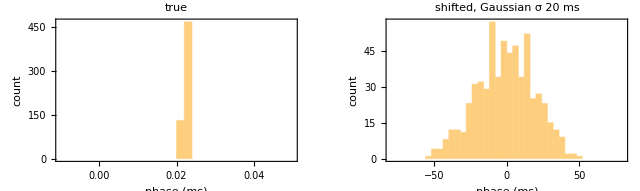

```mathematica
phase[t_] := With[{f = Mod[t, $Ticks]}, If[f > $Ticks/2, f - $Ticks, f]/64000.];
GraphicsRow[{
  Histogram[phase /@ onehz[[All, 1, "nova_time"]], {-0.01, 0.05, 0.002}, Frame -> True, FrameLabel -> {"phase (ms)", "count"}, PlotLabel -> "true"],
  Histogram[phase /@ onehz[[All, 2, "nova_time"]], {-80, 80, 4}, Frame -> True, FrameLabel -> {"phase (ms)", "count"}, PlotLabel -> "shifted, Gaussian σ 20 ms"]}, ImageSize -> 640]
```

The blur hides when within the second each pulse fired. It cannot hide that the pulser is periodic: anyone who knows a signal fires on the second can round each shifted time to the nearest second and so learn that event's offset, as long as the bound is below 500 ms. That reveals nothing about any other event, because offsets are independent, but the times of predictable events are effectively public whatever is done to them.

### 11.2 Order

event_number must stay in the file for inversion, and it numbers events in true order. The order of events is therefore not hidden, only their times. The shifted times themselves can come out of order when events are closer together than the blur:

```mathematica
reorder[sh_] := Module[{bysrc = GroupBy[sh, #["source"] &]},
   N@Mean[Flatten[Values[Map[With[{s = SortBy[#, #["event_number"] &]},
         Boole[Thread[Differences[s[[All, "nova_time"]]] < 0]]] &, bysrc]]]]];
xs = Table[offsetGauss[parseToken[tokG]["secret"], "dts1:gauss:sigma=1280000:cut=3840000", 1280000, 3840000, r["source"], r["event_number"]][[2]], {r, orig}];
sigmas = {0.5, 1, 2, 5, 10, 20, 50, 100, 500/3};
frac = Table[{s, reorder[MapThread[Append[#1, "nova_time" -> #1["nova_time"] + Round[#2 s 64000]] &, {orig, xs}]]}, {s, sigmas}]
```

{{0.5,0.},{1,0.},{2,0.000212857},{5,0.000425713},{10,0.00063857},{20,0.00574713},{50,0.090464},{100,0.174968},{500/3,0.227756}}

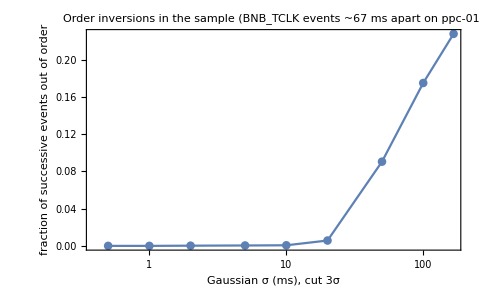

```mathematica
ListLogLinearPlot[frac, Joined -> True, Mesh -> All, Frame -> True, ImageSize -> 480,
 FrameLabel -> {"Gaussian σ (ms), cut 3σ", "fraction of successive events out of order"},
 PlotLabel -> "Order inversions in the sample (BNB_TCLK events ~67 ms apart on ppc-01)"]
```

(The draws here reuse one token's normal variates, scaled to each σ, to isolate the dependence on width.) Up to 1 ms nothing reorders and up to 10 ms fewer than 0.1% of neighbours swap; at 20 ms it is about 0.6%, and by 50 ms about 9%, as the BNB_TCLK events on ppc-01, 67 ms apart, start to cross. σ = 500/3 ms is the widest Gaussian whose 3σ cut fits the 500 ms ceiling. Sorting a shifted file by time therefore does not give the true order, but sorting by event_number does.

### 11.3 Summary

Hidden: each event's time to within the chosen distribution; its sub-second phase; the exact spacing of events (delta is blurred by o_n-o_(n-1)).

Not hidden: event order and counts, types and sources; times of events that are predictable from structure (periodic signals); anything outside the file.

Key reuse: event_number restarts when TCRMonitor restarts, so two events weeks apart can share (source, n) and hence an offset. Inversion is unaffected; an observer who could match such pairs learns that their offsets are equal, not what they are.

Seeds: a seed-derived token is as strong as the seed. Use a generated token when the blur protects something.

## 12. Test vectors

Written to docs/shift/dts1_test_vectors.json for the Python tests: the HMAC and PBKDF2 checks, offsets for edge-case event numbers under both tokens, the near-tie cases of section 8, and the first 500 shifted rows of the sample under each token.

```mathematica
edgeNs = {-1, 0, 1, 2, 3, 178098, 2^31 - 1, 2^31, 2^53, 10^15};
vectors = <|
  "spec" -> "dts1",
  "hmac_rfc4231_case2" -> "5bdcc146bf60754e6a042426089575c75a003f089d2739839dec58b964ec3843",
  "pbkdf2" -> <|"seed" -> "correct horse battery staple", "salt" -> "darpa-spill-shift/dts1", "iterations" -> 1000,
     "secret_hex" -> StringJoin[IntegerString[Normal@pbkdf2SHA256["correct horse battery staple", "darpa-spill-shift/dts1", 1000], 16, 2]]|>,
  "tokens" -> <|"flat" -> tokF, "gauss" -> tokG|>,
  "fingerprints" -> <|"flat" -> fingerprint[tokF], "gauss" -> fingerprint[tokG]|>,
  "offsets" -> Flatten@Table[<|"token" -> name, "source" -> src, "n" -> n,
       "offset" -> offset[If[name == "flat", tokF, tokG], src, n]|>,
      {name, {"flat", "gauss"}}, {src, {"tdu-near-master-ppc-01", "x"}}, {n, edgeNs}],
  "near_ties" -> ties,
  "sample_file" -> "sample_2026-10-12T0000_10min.csv",
  "shifted_sample" -> <|"flat" -> Values /@ shiftedF[[;; 500, {"nova_time", "delta", "pps_offset"}]],
     "gauss" -> Values /@ shiftedG[[;; 500, {"nova_time", "delta", "pps_offset"}]]|>|>;
Export[FileNameJoin[{$dataDir, "dts1_test_vectors.json"}], vectors, "RawJSON"];
Keys[vectors]
```

{spec,hmac_rfc4231_case2,pbkdf2,tokens,fingerprints,offsets,near_ties,sample_file,shifted_sample}